```mathematica
basePath = "/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/";
fileNamesN=FileNames["*.jp*", {basePath<>"NORMAL"}];
fileNamesP=FileNames["*.jp*", {basePath<>"PNEUMONIA"}];
```

```mathematica
imageDimensions=ImageDimensions[Import[#]]&/@Join[fileNamesN,fileNamesP];
```

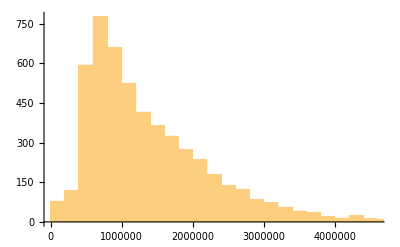

```mathematica
Histogram[Times@@#&/@imageDimensions]
```

```mathematica
fileNamesN//Length
```

1341

```mathematica
fileNamesP[[3683-1341]]
```

/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/PNEUMONIA/person407_virus_811.jpeg

```mathematica
Min[Last/@imageDimensions]
```

127

```mathematica
Min[First/@imageDimensions]
```

384

```mathematica
Select[imageDimensions,Last[#]==127&]
```

{{384,127}}

```mathematica
Position[imageDimensions, {384,127}]
```

{{3683}}

```mathematica
fileNames[[3683]]
```

/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/PNEUMONIA/person407_virus_811.jpeg

```mathematica
img=Import["/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/PNEUMONIA/person407_virus_811.jpeg"]
```

-Graphics-

```mathematica
ClearAll[PreprocessImage];PreprocessImage[img_]:=Module[{hCrop=0.3,vCrop=0.3,targetWidth=512,dwd},
dwd=DiscreteWaveletTransform[HistogramTransform[
ImageAdjust[
ImageCrop[
ImageResize[img,{targetWidth+2hCrop targetWidth,targetWidth+2vCrop targetWidth}],{targetWidth,targetWidth}]
]],
Automatic,2];
ImageAdjust[ImageCrop[ImagePeriodogram[ImageAdjust[dwd[All,"Image"][[4,2]]]],{targetWidth/8,targetWidth/8}],{1.5,0,1},{0.5,1}]
];
```

```mathematica
batchSize=1;
idx=1341;
Print[fileNamesN[[(idx-1)batchSize+1]]];
Print[fileNamesP[[(idx-1)batchSize+1]]];
GraphicsGrid[{
Join[PreprocessImage[Import[#]]&/@fileNamesN[[(idx-1)batchSize+1;;idx batchSize]],
PreprocessImage[Import[#]]&/@fileNamesP[[(idx-1)batchSize+1;;idx batchSize]]]
}]
```

/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/NORMAL/NORMAL2-IM-1423-0001.jpeg

/Users/zhuvikin/workspace/ai-university/data/chest_xray/train/PNEUMONIA/person1626_bacteria_4291.jpeg

-Graphics-